# Model Fit and Amplification

```mathematica
Clear["Global`*"]
```

### Data

```mathematica
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n] (*repeat integer function*)
rmblank[data_]:=Delete[data,Partition[Position[data,""][[All,1]],1]] (*function to remove blanks from data*)
colors={h->ColorData[97][2],s->ColorData[97][1]}; (*Universal Colors*)
th={1,2,3,4,5,6,7,8}; (*host time steps*)
ts={0,1,2,4,6,8}; (*symbiont time steps*)
tb={0,0,0,1,6,8,11,12}; (* # of tissueballs per host time step*)
ys=63 1/10^12 1/12.01 ; (*symbiont biomass conversions*)
yh[area_]:=10^-0.7013(2 √(area/Pi))^2.4124 1/1000 0.55 1/12.01 (*host biomass conversions*)
sadj[data_]:= 2/3 Pi(√(data/Pi))^3 0.16 1/1000 0.55 1/12.01 (*tissue-ball biomass conversion*)
dataa=Import[NotebookDirectory[]<>"Peng_et_al._supplemental_data_0403_adj.xlsx"]; (*import complete data*)

(*extract data by treatment*)
dataf=rmblank[Flatten[{Transpose[{{repeat[#,12]},dataa[[2]][[2;;13]][[All,#+3]]}]&/@th},2]]; (*aposymbiotic fed host*)
datif=rmblank[Flatten[{Transpose[{{repeat[#,12]},dataa[[2]][[14;;25]][[All,#+3]]}]&/@th},2]]; (*innoculated fed host*)
datas=rmblank[Flatten[{Transpose[{{repeat[#,12]},dataa[[2]][[26;;37]][[All,#+3]]}]&/@th},2]]; (*aposymbiotic starved host*)
datis=rmblank[Flatten[{Transpose[{{repeat[#,12]},dataa[[2]][[38;;49]][[All,#+3]]}]&/@th},2]]; (*inoculated starved host*)
datisa=rmblank[Flatten[{Transpose[{{repeat[ts[[#]],5]},dataa[[3]][[3;;7]][[All,#+2]]}]&/@Range[1,6,1]},2]]; (*innoculated starved symbiont*)
datifa=rmblank[Flatten[{Transpose[{{repeat[ts[[#]],5]},dataa[[3]][[9;;13]][[All,#+2]]}]&/@Range[1,6,1]},2]]; (*innoculated fed symbiont*)


dat[treatment_,species_]:=Piecewise[{{datas, treatment=="as"}, {dataf, treatment=="af"}, {datisa, treatment=="is"∧species=="s"}, {datis, treatment=="is"∧species=="h"}, {datifa, treatment=="if"∧species=="s"}, {datif, treatment=="if"∧species=="h"}}](*original units data function*)
tbc=If[dat["is","h"][[#,1]]≥4∧MemberQ[(*tissue ball conversion*)
TakeSmallest[
dat["is","h"][[#,2]]&/@Position[dat["is","h"],
dat["is","h"][[#,1]]][[All,1]],
Min[
tb[[dat["is","h"][[#,1]]]],
Length[Position[dat["is","h"],
dat["is","h"][[#,1]]][[All,1]]]]],
dat["is","h"][[#,2]]],
{dat["is","h"][[#,1]],sadj[dat["is","h"][[#,2]]]},
{dat["is","h"][[#,1]],yh[dat["is","h"][[#,2]]]}]&/@Range[1,Length[dat["is","h"]]];
adj[treatment_,species_]:=(*biomass unit function*)Piecewise[{{{dat["af","h"][[#,1]],yh[dat["af","h"][[#,2]]]}&/@Range[1,Length[dat["af","h"]]], treatment=="af"∧species=="h"}, {{dat["if","h"][[#,1]],yh[dat["if","h"][[#,2]]]}&/@Range[1,Length[dat["if","h"]]], treatment=="if"∧species=="h"}, {{dat["as","h"][[#,1]],yh[dat["as","h"][[#,2]]]}&/@Range[1,Length[dat["as","h"]]], treatment=="as"∧species=="h"}, {tbc, treatment=="is"∧species=="h"}, {{dat["if","s"][[#,1]],ys dat["if","s"][[#,2]]}&/@Range[1,Length[dat["if","s"]]], treatment=="if"∧species=="s"}, {{dat["is","s"][[#,1]],ys dat["is","s"][[#,2]]}&/@Range[1,Length[dat["is","s"]]], treatment=="is"∧species=="s"}}] 
means[treat_,sp_]:=(*meanbiomass unit function*)Piecewise[{{Transpose[{th,Mean[adj["as","h"][[#,2]]&/@Flatten[Position[adj["as","h"][[All,1]],#],1]]&/@th}], treat=="as"∧sp=="h"}, {Transpose[{th,Mean[adj["af","h"][[#,2]]&/@Flatten[Position[adj["af","h"][[All,1]],#],1]]&/@th}], treat=="af"∧sp=="h"}, {Transpose[{th,Mean[adj["is","h"][[#,2]]&/@Flatten[Position[adj["is","h"][[All,1]],#],1]]&/@th}], treat=="is"∧sp=="h"}, {Transpose[{th,Mean[adj["if","h"][[#,2]]&/@Flatten[Position[adj["if","h"][[All,1]],#],1]]&/@th}], treat=="if"∧sp=="h"}, {Transpose[{ts,Mean[adj["is","s"][[#,2]]&/@Flatten[Position[adj["is","s"][[All,1]],#],1]]&/@ts}], treat=="is"∧sp=="s"}, {Transpose[{ts,Mean[adj["if","s"][[#,2]]&/@Flatten[Position[adj["if","s"][[All,1]],#],1]]&/@ts}], treat=="if"∧sp=="s"}}]
```

### Model

```mathematica
tmax=8; (* 8-week time set *)
parsFixed={nhn->0.18,nsn->0.13}; (*fixed parameters*)
sim[pars_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f},(*Simulation*)
f=s[t](a h[t])/(s[t]+a w h[t]);(*equation 13*)
jsc=p s[t]; (*equation 6*)
jsn=yn nhn f; (*equation 5*)
jhc= p s[t]-Min[jsc,nsn^-1 jsn]+rc h[t]^(2/3);(*equations 10 and 11*)
jhn=rn  h[t]^(2/3);(*equation 9*)
jsg=Min[jsc,nsn^-1 jsn]; (*equation 3*)
jst=ds s[t]; (*equation 4*)
jhg=Min[jhc,nhn^-1 jhn];(*equation 7*)
jht=dh h[t] + f;(*equation 8*)
Quiet@NDSolve[
{
s'[t]==jsg-jst,(*equation 1*)
h'[t]==jhg-jht,(*equation 2*)
s[0]==s0,
h[0]==h0
}/.pars,
{s,h},
{t,0,tmax},Method->{Automatic,"DiscontinuityProcessing"->None},WorkingPrecision->20][[1]]];
pars[treatment_]:=(*parameter choices function*)Piecewise[{{Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->0,h0->h0X},parsFixed], treatment=="as"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->0,h0->h0X},parsFixed], treatment=="af"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->s0X,h0->h0X},parsFixed], treatment=="if"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->s0X,h0->h0X},parsFixed], treatment=="is"}}]
```

### Fit

```mathematica
parsStartX={aX->0.071,wX->0.0028,pX->20,ynX->0.062,dsX->0.7810372609047624,dhX->0.13,h0X->6.5*^-6,s0X->1.0*^-10,rcX->0.01,rnX->.01}; (*initial parameter guesses*)
parsToFitAll=parsStartX[[All,1]]; (* parameters to fit*)
constraints=Join[#>10^-10&/@parsToFitAll,{ynX<1}]; (*parameter constraints*)
ssq[pars_?(AllTrue[#[[All,2]],NumberQ]&),datAndfs_]:=
With[{sol=sim[pars],dat=datAndfs[[1]],f=datAndfs[[2]]},Sum[(f[d[[1]]]-d[[2]]/. sol)^2,{d,dat}]];(*sum of squared error, equation B.2*)
loglh1:=Sum[Length[adj[treat,"h"]]/2 Log[ssq[pars[treat],{adj[treat,"h"],h}]],{treat,{"as","af","if","is"}}]+Sum[Length[adj[treat,"s"]]/2 Log[ssq[pars[treat],{adj[treat,"s"],s}]],{treat,{"if","is"}}]; (*log-likelihood, equation B.3*)
fitlh1=Quiet[NMinimize[
{loglh1,constraints},Join[{#},{.5,2}#/.parsStartX]&/@parsToFitAll,
Method->{"NelderMead","PostProcess"->False},MaxIterations->10^6]] (*minimixe log-likelihood over parameter constraints*)
```

{-4424.16,{aX→0.0724317,wX→0.0026143,pX→27.7005,ynX→0.060193,dsX→0.770998,dhX→0.126196,h0X→6.50294×10^-6,s0X→1.02278×10^-10,rcX→0.00999209,rnX→0.0146453}}

### Fit Plot

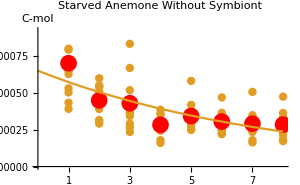
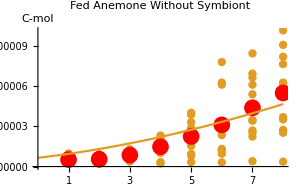
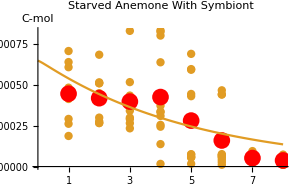
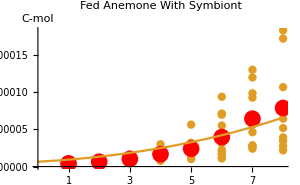
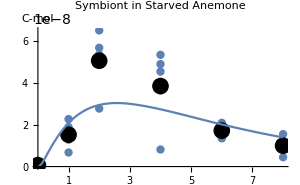
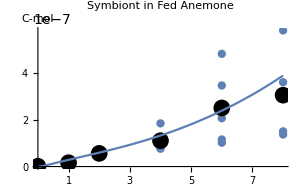
-Graphics-WeeksA
-Graphics-WeeksB | •    Anemone
•    Symbiont
•    Mean Anemone
•    Mean Symbiont
—    Model Anemone
—    Model Symbiont
-Graphics-WeeksC
-Graphics-WeeksD | -Graphics-WeeksE
-Graphics-WeeksF

/Users/JakobK-R/Dropbox/Peng_Anemone/Paper_Upload/fitplot.jpg

```mathematica
sol[treat_]:=Piecewise[{{sim[pars["as"]/.fitlh1[[2]]], treat=="as"}, {sim[pars["af"]/.fitlh1[[2]]], treat=="af"}, {sim[pars["is"]/.fitlh1[[2]]], treat=="is"}, {sim[pars["if"]/.fitlh1[[2]]], treat=="if"}}] (*simulations for each tratment at figged parameter values*)
label=PlotLabel->Style[name,15,FontFamily->"Times New Roman",FontColor->"Black"];(*label*)
(*all treatment and data fit plots*)
asa=Panel[Labeled[Show[
ListPlot[{adj["as","h"]},PlotStyle->{{h/.colors,PointSize[0.02]}},label/.name->"Starved Anemone Without Symbiont",AxesOrigin->{0,0},ImagePadding->{{36,20},{10,15}},Ticks->{Range[1,8],Automatic}],
ListPlot[{means["as","h"]},PlotStyle->{{Red,PointSize[0.04]}}],
Plot[Evaluate[h[t]/.sol["as"]],{t,0,tmax},PlotStyle->(h/.colors),PlotRange->Full],AxesLabel->{Null,Style["C-mol",FontFamily->"Times New Roman",FontColor->Black]},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->300],Style["Weeks",10,FontFamily->"Times New Roman",FontColor->Black]],Style["A",Bold,FontFamily->"Times New Roman",FontSize->20],{{Left,Top}},Appearance->Frame,Background->White];
afa=Panel[Labeled[Show[
ListPlot[{adj["af","h"]},PlotStyle->{{h/.colors,PointSize[0.02]}},label/.name->"Fed Anemone Without Symbiont",PlotRange->Full,AxesOrigin->{0,0},ImagePadding->{{36,20},{10,15}},Ticks->{Range[1,8],Automatic}],
ListPlot[{means["af","h"]},PlotStyle->{{Red,PointSize[0.04]}}],
Plot[Evaluate[h[t]/.sol["af"]],{t,0,tmax},PlotStyle->(h/.colors),PlotRange->Full],AxesLabel->{Null,Style["C-mol",FontFamily->"Times New Roman",FontColor->Black]},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->300],Style["Weeks",10,FontFamily->"Times New Roman",FontColor->Black]],Style["B",Bold,FontFamily->"Times New Roman",FontSize->20],{{Left,Top}},Appearance->Frame,Background->White];
ifa=Panel[Labeled[Show[
ListPlot[{adj["if","h"]},PlotStyle->{{h/.colors,PointSize[0.02]}},label/.name->"Fed Anemone With Symbiont",PlotRange->Full,AxesOrigin->{0,0},ImagePadding->{{36,20},{10,15}},Ticks->{Range[1,8],Automatic}],
ListPlot[{means["if","h"]},PlotStyle->{{Red,PointSize[0.04]}}],
Plot[Evaluate[h[t]/.sol["if"]],{t,0,tmax},PlotStyle->(h/.colors),PlotRange->Full],AxesLabel->{Null,Style["C-mol",FontFamily->"Times New Roman",FontColor->Black]},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->300],Style["Weeks",10,FontFamily->"Times New Roman",FontColor->Black]],Style["D",Bold,FontFamily->"Times New Roman",FontSize->20],{{Left,Top}},Appearance->Frame,Background->White];
ifs=
Panel[Labeled[Show[
ListPlot[{adj["if","s"]},PlotStyle->{{PointSize[.02],s/.colors}},label/.name->"Symbiont in Fed Anemone ",PlotRange->Full,AxesOrigin->{0,0},ImagePadding->{{36,20},{10,15}},Ticks->{Range[1,8],Automatic}],
ListPlot[{means["if","s"]},PlotStyle->{{PointSize[.04],Black}}],
Plot[Evaluate[s[t]/.sol["if"]],{t,0,tmax},PlotStyle->(s/.colors),PlotRange->Full],AxesLabel->{Null,Style["C-mol",FontFamily->"Times New Roman",FontColor->Black]},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->300],Style["Weeks",10,FontFamily->"Times New Roman",FontColor->Black]],Style["F",Bold,FontFamily->"Times New Roman",FontSize->20],{{Left,Top}},Appearance->Frame,Background->White];
isa=
Panel[Labeled[Show[
ListPlot[{adj["is","h"]},PlotStyle->{{h/.colors,PointSize[0.02]}},label/.name->"Starved Anemone With Symbiont",PlotRange->Full,AxesOrigin->{0,0},ImagePadding->{{36,20},{10,15}},Ticks->{Range[1,8],Automatic}],
ListPlot[{means["is","h"]},PlotStyle->{{Red,PointSize[0.04]}}],
Plot[Evaluate[h[t]/.sol["is"]],{t,0,tmax},PlotStyle->(h/.colors),PlotRange->Full],AxesLabel->{Null,Style["C-mol",FontFamily->"Times New Roman",FontColor->Black]},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->300],Style["Weeks",10,FontFamily->"Times New Roman",FontColor->Black]],Style["C",Bold,FontFamily->"Times New Roman",FontSize->20],{{Left,Top}},Appearance->Frame,Background->White];
iss=
Panel[Labeled[Show[
ListPlot[{adj["is","s"]},PlotStyle->{{PointSize[.02],s/.colors}},label/.name->"Symbiont in Starved Anemone ",PlotRange->Full,AxesOrigin->{0,0},ImagePadding->{{36,20},{10,15}},Ticks->{Range[1,8],Automatic}],
ListPlot[{means["is","s"]},PlotStyle->{{PointSize[.04],Black}}],
Plot[Evaluate[s[t]/.sol["is"]],{t,0,tmax},PlotStyle->(s/.colors),PlotRange->Full],AxesLabel->{Null,Style["C-mol",FontFamily->"Times New Roman",FontColor->Black]},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->300],Style["Weeks",10,FontFamily->"Times New Roman",FontColor->Black]],Style["E",Bold,FontFamily->"Times New Roman",FontSize->20],{{Left,Top}},Appearance->Frame,Background->White];
(*plot label*)
fitlabel=Column[
{Row[{Style[•,25,h/.colors],Style["    Anemone",20,FontFamily->"Times New Roman"]}],
Row[{Style[•,25,s/.colors],Style["    Symbiont",20,FontFamily->"Times New Roman"]}],
Row[{Style[•,25,Red],Style["    Mean Anemone",20,FontFamily->"Times New Roman"]}],
Row[{Style[•,25,Black],Style["    Mean Symbiont",20,FontFamily->"Times New Roman"]}],
Row[{Style["—",25,h/.colors,FontSize->Large],Style["    Model Anemone",20,FontFamily->"Times New Roman"]}],
Row[{Style["—",25,s/.colors,FontSize->Large],Style["    Model Symbiont",20,FontFamily->"Times New Roman"]}]}];
tl=Column[{asa,afa}];(*top left*) 
br=Column[{iss,ifs}];(*bottom right*)
bl=Column[{isa,ifa}];(*bottom left*)
fitplot=Grid[{{tl,fitlabel},{bl,br}}](*Figure 2*)
Export[NotebookDirectory[]<>"fitplot.jpg",fitplot]
```

### Amplification Plot

/Users/JakobK-R/Dropbox/Peng_Anemone/Paper_Upload/ampplot.jpg

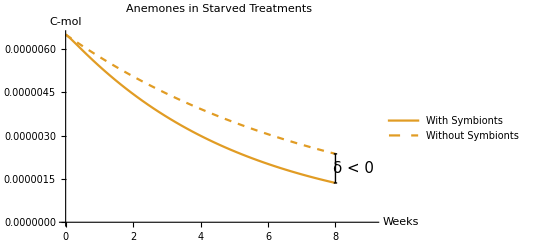
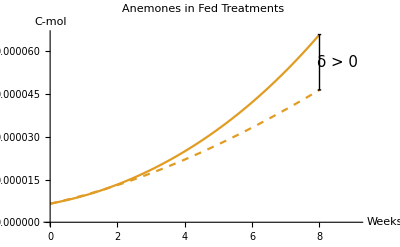
-Graphics-A
-Graphics-B

```mathematica
(*Figure 3*)
ampplot=Quiet[Legended[
Grid[{
{Panel[Plot[{Evaluate[h[t]/.sim[pars["is"]/.fitlh1[[2]]]],Evaluate[h[t]/.sim[pars["as"]/.fitlh1[[2]]]]},{t,0,tmax},PlotStyle->{{h/.colors},{h/.colors,Dashed}},PlotRange->{{0,9.1},Automatic},AxesLabel->{"Weeks","C-mol"}, AxesOrigin->{0,0},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->400,ImagePadding->{{40,Automatic},{Automatic,Automatic}},PlotLabel->Style["Anemones in Starved Treatments",FontSize->16],
Epilog->
{Thick,Line[{{8,Evaluate[h[8]/.sim[pars["is"]/.fitlh1[[2]]]]
},{8,Evaluate[h[8]/.sim[pars["as"]/.fitlh1[[2]]]]}}],
Thick,Line[{{7.95,Evaluate[h[8]/.sim[pars["is"]/.fitlh1[[2]]]]},{8.05,Evaluate[h[8]/.sim[pars["is"]/.fitlh1[[2]]]]}}],
Thick,Line[{{7.95,Evaluate[h[8]/.sim[pars["as"]/.fitlh1[[2]]]]},{8.05,Evaluate[h[8]/.sim[pars["as"]/.fitlh1[[2]]]]}}],
Text[Style["δ < 0",FontSize->15],{8.54,(Evaluate[h[8]/.sim[pars["is"]/.fitlh1[[2]]]]+Evaluate[h[8]/.sim[pars["as"]/.fitlh1[[2]]]])/2}]}],Style["A",Bold,FontFamily->"Times New Roman",FontSize->25],{{Left,Top}},Appearance->Frame,Background->White]},
{Panel[Plot[{Evaluate[h[t]/.sim[pars["if"]/.fitlh1[[2]]]],Evaluate[h[t]/.sim[pars["af"]/.fitlh1[[2]]]]},{t,0,tmax},PlotStyle->{{h/.colors},{h/.colors,Dashed}},PlotRange->{{0,9.1},Automatic},AxesLabel->{"Weeks","C-mol"}, AxesOrigin->{0,0},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->400,ImagePadding->{{40,Automatic},{Automatic,Automatic}},PlotLabel->Style["Anemones in Fed Treatments",FontSize->16],
Epilog->
{Thick,Line[{{8,Evaluate[h[8]/.sim[pars["if"]/.fitlh1[[2]]]]},{8,Evaluate[h[8]/.sim[pars["af"]/.fitlh1[[2]]]]}}],
Thick,Line[{{7.95,Evaluate[h[8]/.sim[pars["if"]/.fitlh1[[2]]]]},{8.05,Evaluate[h[8]/.sim[pars["if"]/.fitlh1[[2]]]]}}],
Thick,Line[{{7.95,Evaluate[h[8]/.sim[pars["af"]/.fitlh1[[2]]]]},{8.05,Evaluate[h[8]/.sim[pars["af"]/.fitlh1[[2]]]]}}],
Text[Style["δ > 0",FontSize->15],{8.54,(Evaluate[h[8]/.sim[pars["if"]/.fitlh1[[2]]]]+Evaluate[h[8]/.sim[pars["af"]/.fitlh1[[2]]]])/2}]}],Style["B",Bold,FontFamily->"Times New Roman",FontSize->25],{{Left,Top}},Appearance->Frame,Background->White]}}
],
Placed[LineLegend[{h/.colors,{h/.colors,Dashed}},{"With Symbionts","Without Symbionts"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15}],Right]]]
Export[NotebookDirectory[]<>"ampplot.jpg",ampplot]
```